# Linguistic Universal

### Shared Concepts

Language is what we use to store & pass knowledge , so similarities between languages may help us to understand the processes of cognition and perception.
All of those can be divided into absolute & implicational. The first group is relatively small, the second one is much smaller and generally describes features shared between languages of geographically & chronologically close cultures.

What are the examples of absolute features?
All languages have nouns and verbs.  // use computations
All languages have pronouns.

Morphology is the study of words, how they are formed, and their relationship to other words in the same language.
Phonology is a branch of linguistics concerned with the systematic organization of sounds in spoken languages and signs in sign languages. 
	All spoken languages have consonants and vowels. // use computations 
Syntax is the set of rules, principles, and processes that govern the structure of sentences (sentence structure) in a given language, usually including word order.
Semantics is the linguistic and philosophical study of meaning in language. Branch of this is “lexical semantics”.
	The concept of morpheme -- the minimal unit of form and meaning -- arises naturally in the analysis of every language.
	The concept of word is trickier. There are at least two troublesome issues: making the distinction between words and phrases, and the status of certain grammatical formatives known as clitics.

```mathematica
Min[Map[EntityValue[#, "Pronouns"] &, {LinguisticAssistant, LinguisticAssistant}]]
```

Min[Missing[NotAvailable],he→{er},she→{sie},they→{man,sie},we→{wir},you→{dich,dir,du,euch,Ihnen,ihr,sich,Sie}]

### Swadesh Corpora

Concepts above primarily describe structural similarities between languages, but in many cases even lexic shows the same similarities. The Swadesh lists were compiled specifically for those purposes - for historical-comparative linguistics. It allows researchers to quantify the interrelatedness of those languages. 

Lets find the distance between every single language and build and show a graph.
Remove diactrics !and non alpha chars.
For that compute the edit distance for every word Wi in languages La, Lb, and sum Wi.

```mathematica
dataSwadesh = ResourceData["Swadesh Lists"];
```

```mathematica
allLangs = Take[Keys[dataSwadesh], 5];
primaryWords = DeleteDuplicates[Flatten[Keys[Values[dataSwadesh]]]]
langsCount = Length[allLangs];
```

Dataset[<>]

```mathematica
WordsTranslatedTo[targetLangIdx_Integer]:=Keys[dataSwadesh[[targetLangIdx]]];
WordsTranslatedTo[targetLangAIdx_Integer, targetLangBIdx_Integer] := Intersection[ WordsTranslatedTo[targetLangAIdx],WordsTranslatedTo[targetLangBIdx]];
TranslationsOfWordsTo[wordsInEng_List, targetLangIdx_Integer]:=Lookup[dataSwadesh[[targetLangIdx]], wordsInEng];
```

```mathematica
SimilarityOfWordsPair[wordsPair_]:=DamerauLevenshteinDistance[wordsPair[[1]], wordsPair[[2]]];
SimilarityOfTranslationSets[wordsA_List, wordsB_List] := Min[Map[SimilarityOfWordsPair, Tuples[{ wordsA, wordsB }]]];
SimilarityOfLanguages[langIdxA_Integer, langIdxB_Integer] := Module[{sharedInEng, translatedToA, translatedToB, distancesPerTranslatin},
(* First we need to extract words that were translated to both languages. *)
sharedInEng = WordsTranslatedTo[langIdxA, langIdxB];
(* Then we need to translate those 2 separately and find how close *)
translatedToA = TranslationsOfWordsTo[sharedInEng, langIdxA];
translatedToB = TranslationsOfWordsTo[sharedInEng, langIdxB];
distancesPerTranslatin = MapThread[SimilarityOfTranslationSets,{translatedToA,translatedToB}];
Mean[distancesPerTranslatin]
];
```

```mathematica
wordsShared = MatrixForm[Table[SimilarityOfLanguages[i, j],{i,langsCount},{j,langsCount}]];
```

MapThread::mptd: Object TranslationsOfWordsTo[Dataset[«104»],1] at position {2, 1} in MapThread[SimilarityOfTranslationSets,{TranslationsOfWordsTo[Dataset[«104»],1],TranslationsOfWordsTo[Dataset[«104»],1]}] has only 0 of required 1 dimensions.

MapThread::mptd: Object TranslationsOfWordsTo[Dataset[«90»],1] at position {2, 1} in MapThread[SimilarityOfTranslationSets,{TranslationsOfWordsTo[Dataset[«90»],1],TranslationsOfWordsTo[Dataset[«90»],2]}] has only 0 of required 1 dimensions.

MapThread::mptd: Object TranslationsOfWordsTo[Dataset[«100»],1] at position {2, 1} in MapThread[SimilarityOfTranslationSets,{TranslationsOfWordsTo[Dataset[«100»],1],TranslationsOfWordsTo[Dataset[«100»],3]}] has only 0 of required 1 dimensions.

General::stop: Further output of MapThread::mptd will be suppressed during this calculation.

### Full European Lexicon

Swadesh list is comprised of just 100 predefined keywords, while modern languages often have (/*code*/) words. So lets jump into lexicostatistics (the quantitative assessment of the genealogical relatedness of languages).

```mathematica
(* Pull some popular European languages *)
langs = { "English", "German" , "French", "Spanish", "Italian", "Polish", "Hungarian" , "Danish", "Swedish", "Finnish", "Dutch", "Portuguese"};
langsCount = Length[langs];
```

```mathematica
LanguageData["English"]["Dataset"];
```

```mathematica
Language["English"]["Dataset"]
```

```mathematica
(* Lets see how connected are the words *)
```

```mathematica
WordsIn[langName_] := Take[ WordList[Language->langName] // ToLowerCase // RemoveDiacritics, 10000];
```

```mathematica
wordsPerLang = Map[WordsIn, langs];
```

```mathematica
wordsCountsPerLang = Map[Length, wordsPerLang];
```

```mathematica
CountSame[langWordsA_, langWordsB_] := Length[Intersection[langWordsA,langWordsB ]];
CountSame[langIdxA_Integer, langIdxB_Integer] := CountSame[wordsPerLang[[langIdxA]],wordsPerLang[[langIdxB]] ];
```

```mathematica
wordsShared = MatrixForm[Table[CountSame[i, j],{i,langsCount},{j,langsCount}]];
```

```mathematica
%338
```

(9998 | 177 | 325 | 118 | 58 | 232 | 82 | 56 | 149 | 4 | 64 | 19
177 | 9943 | 98 | 39 | 23 | 200 | 98 | 53 | 213 | 5 | 29 | 6
325 | 98 | 9606 | 110 | 150 | 100 | 44 | 90 | 163 | 1 | 80 | 43
118 | 39 | 110 | 9949 | 211 | 211 | 112 | 14 | 97 | 6 | 16 | 335
58 | 23 | 150 | 211 | 9831 | 81 | 47 | 6 | 39 | 1 | 7 | 50
232 | 200 | 100 | 211 | 81 | 9755 | 208 | 58 | 174 | 8 | 33 | 21
82 | 98 | 44 | 112 | 47 | 208 | 9815 | 30 | 150 | 4 | 13 | 15
56 | 53 | 90 | 14 | 6 | 58 | 30 | 9909 | 232 | 9 | 125 | 20
149 | 213 | 163 | 97 | 39 | 174 | 150 | 232 | 9805 | 5 | 40 | 14
4 | 5 | 1 | 6 | 1 | 8 | 4 | 9 | 5 | 9997 | 4 | 2
64 | 29 | 80 | 16 | 7 | 33 | 13 | 125 | 40 | 4 | 9987 | 16
19 | 6 | 43 | 335 | 50 | 21 | 15 | 20 | 14 | 2 | 16 | 9077)

```mathematica
g = WeightedAdjacencyGraph[langs, %69, DirectedEdges->False, VertexLabels->"Name"];
SetProperty[g, GraphLayout->"CircularEmbedding"];
SetProperty[g,EdgeStyle->Thread[EdgeList[g]->(Directive[Thick,ColorData[1,#]]&/@ Rescale[PropertyValue[g,EdgeWeight]])]];
```

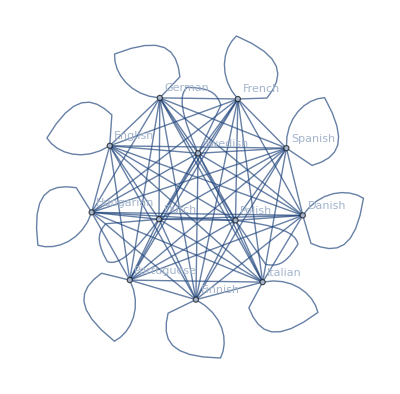

```mathematica
%334
```

```mathematica
(* How can we measure the edit distance? *)
```

The Levenstein distance computations are very costly and ideally we should run the for every pair of words in the language.